## Cylindrical Cavity Resonances

This notebook is associated with the results presented in Chapter 3  of the Master Thesis  “Analogue Black hole binaries”.

### Clean Variables

In case you run into any of Mathematica problems, just clean all variables and go at it again

```mathematica
(*Clear all variables *)
ClearAll["Global`*"]
```

### Eigenfunction

As pointed out in the document, we wish to calculate the eigenfrequencies w given by the equation (EQUATION). The parameters we have are:

	m : Azimuthal number
	Ω: Cylinder rotation speed 
	R0: Outer cavity radius (in units of the inner cylinder radius)
	
We begin then by defining the function whose zeros we need to find:

```mathematica
(*Eigenfunction*)
f[R_?NumericQ , m_?NumericQ , Ω_?NumericQ,Z_]:= (2*I*(w-m*Ω)*BesselJ[m,w]+w*Z*(BesselJ[m-1,w]-BesselJ[m+1,w]))/(2*I*(w-m*Ω)*BesselY[m,w]+w*Z*(BesselY[m-1,w]-BesselY[m+1,w]))-(BesselJ[m-1,R*w]-BesselJ[m+1,R*w])/(BesselY[m-1,R*w]-BesselY[m+1,R*w])
```

This first function fixes the inner cylinder size to be equal to unity. We can have the more generic scenario as well:

```mathematica
(*Eigenfunction*)
f2[Ri_?NumericQ,R_?NumericQ , m_?NumericQ , Ω_?NumericQ,Z_]:= (2*I*(w-m*Ω)*BesselJ[m,Ri*w]+w*Z*(BesselJ[m-1,Ri*w]-BesselJ[m+1,Ri*w]))/(2*I*(w-m*Ω)*BesselY[m,Ri*w]+w*Z*(BesselY[m-1,Ri*w]-BesselY[m+1,Ri*w]))-(BesselJ[m-1,R*w]-BesselJ[m+1,R*w])/(BesselY[m-1,R*w]-BesselY[m+1,R*w])
```

We will work with the first one in this notebook.

### Finding roots - Helper functions

To find the eigenvalues of the above equation we will need to do some fine tuning by hand, but before getting to that point we can use a brute force method to find a set of roots. 
The function below takes in a function and some parameters defining a square grid in the complex plane to search for zeros of the function in that rectangle.
Depending on the parameters chosen, the function may take some time (minutes) to run and will return a large list of zeros (many of them repeated) from which we will get exact values.

```mathematica
(*Function to get Zeros*)
get…zero…list[f_  , xmin_ ,xmax_,ymin_,ymax_,dx_,dy_]:=
Block[

	(*Clear Variables*)
	{list ,zerolist,flist, final…zeros , ylist},

	(* Create list of initial points *)
	list = Flatten[Table[i+ ⅈ*j,{i,xmin,xmax,dx},{j,ymin,ymax,dy}]];

	(*Create empty list to store roots*)
	zerolist = List[];

	(*Find Root*)
	Quiet[
	For[k=1,k<Length[list],k++,
	AppendTo[zerolist,w/.FindRoot[f==0,{w,list[[k]]},  MaxIterations-> 10]];
	]
	];

(*Check if they are roots*)
flist = Table[If[ Abs[f/.w-> zerolist[[k]]]<10^-7&&xmin<Re[zerolist[[k]]]<xmax &&ymin<Im[zerolist[[k]]]<ymax,1.0,0.0,0.0],{k,1,Length[list]-1}];

(*Return the found roots*)
final…zeros = Table[    zerolist[[k]]*flist[[k]],{k,1,Length[list]-1}];

(*Delete 0 values and duplicate roots*)
ylist = DeleteCases[final…zeros,0.+0.I];
DeleteDuplicates[ylist,Abs[#1-#2]<0.0001&]

]
```

```mathematica
(*Search for other functions zeros starting at these zeros*)
get…zero…list…from[f_  , start…values_]:=
Block[

	(*Clear Variables*)
	{list ,zerolist,flist, final…zeros},

	(*Create empty list to store roots*)
	zerolist = List[];

	(*Find Root*)
	Quiet[
	For[k=1,k<Length[start…values]+1,k++,
	AppendTo[zerolist,w/.FindRoot[f==0,{w,start…values[[k]]},  MaxIterations-> 100]];
	]
	];

(*Check if they are roots*)
flist = Table[If[ Abs[f/.w-> zerolist[[k]]]< 10^-8,1.0,0.0,0.0],{k,1,Length[start…values]}];

(*Return the found roots*)
final…zeros = Table[    zerolist[[k]]*flist[[k]],{k,1,Length[start…values]}];

DeleteCases[final…zeros,0.+0.I]
]
```

### Finding roots (and rotation dependence)

The procedure to find the zeros for a given set of parameters can be obtained by the following method:

	1. Choose initial set of parameters from where you want to start your search 
	2. Vary the parameters one by one until you get to the final parameters

In the case below, we start with a set of parameters for the azimuthal mode m, the Impedance value Z , and the cavity size R0. We define the region we want to probe and do a brute force search from which we can extract a set of zeros from where our search will proceed.
This section is an example one. It can easily be adapted to any case you may need.

```mathematica
(*Function parameters*)
m = 2;
Ω = 0.35;
R1 = 2.0
Rc =38;
Z = 0.2;

(*Region to search for zeros*)
xmin = 0.01;
xmax = 1.3;
ymin = -0.01;
ymax =0.01;
dx =0.01;
dy=0.005;

(*Find zeros*)
startingZeros = get…zero…list[f2[R1,Rc , m  , 0.0, Z],xmin , xmax ,ymin ,ymax ,dx ,dy];
```

2.

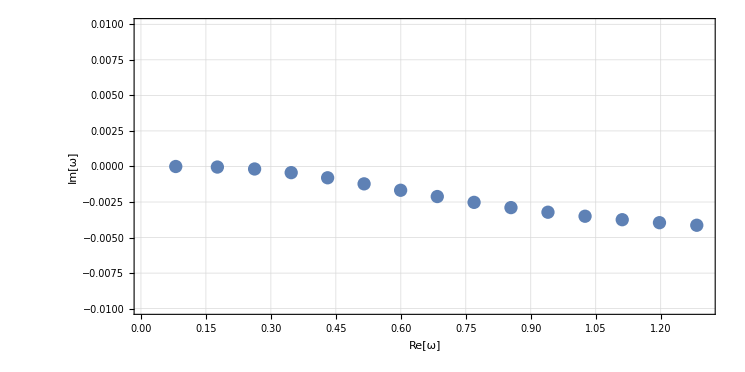

```mathematica
(*Plot First Zeros*)
ComplexListPlot[
	startingZeros, 
	AspectRatio->1/2,
	PlotRange->{{xmin,xmax},{-0.01,0.01}},
	PlotTheme->"Detailed",
	FrameLabel->{"Re[ω]","Im[ω]"}]
```

We now can begin, for example, by varying the rotation speed of the cylinder. We define the initial and final speeds and the number of points we want between the two values. We then find, iteratively, the new zeros of the function.

```mathematica
(*Initial zeros*)
list…of…Omega…zeros = List[startingZeros];

(*Rotation Parameters*)
OmegaI = 0.0;
OmegaF = 0.35;
NOmega = 120;
dOmega = (OmegaF -OmegaI)/(NOmega-1);
Omega…list = Table[OmegaI + (i-1)*dOmega,{i,1,NOmega}];
```

```mathematica
(*Search for sucessive zeros with different alpha parameters*)
Do[
AppendTo[
list…of…Omega…zeros, 
get…zero…list…from[f2[R1,Rc , m  , Omega…list[[i]], Z], list…of…Omega…zeros[[-1]]]]
,{i,1,NOmega}
]
```

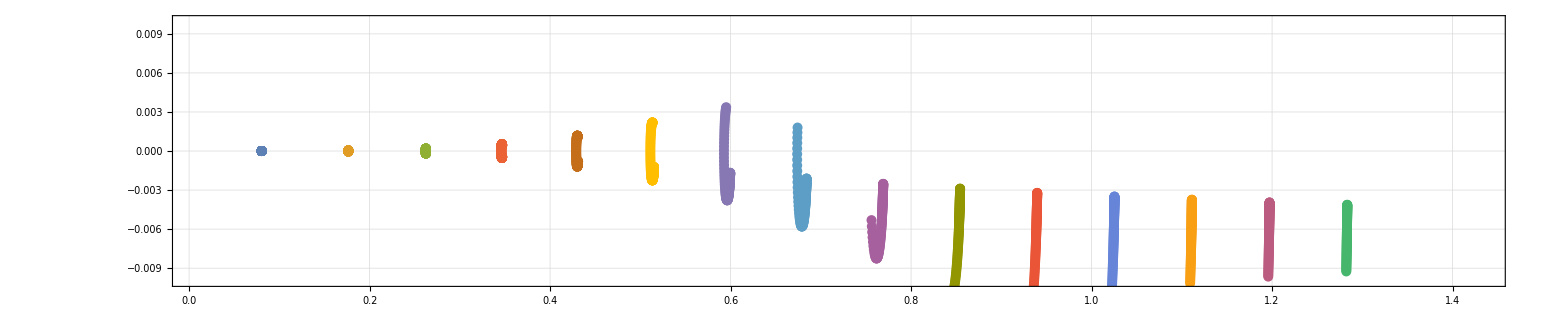

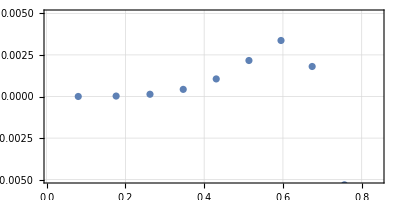

```mathematica
(*Plot Result*)
ComplexListPlot[
Transpose[list…of…Omega…zeros],
AspectRatio->1/5,
PlotRange->{{xmin,1.1*xmax},{-0.01,0.01}},
PlotTheme->"Detailed"]

(*Plot detail*)
ComplexListPlot[
list…of…Omega…zeros[[-1]],
AspectRatio->1/2,
ImageSize->Full,
PlotRange->{{xmin,m*OmegaF*1.2},{-0.005,0.005}},
PlotTheme->"Detailed"]
```

```mathematica
Table[NumberForm[list…of…Omega…zeros[[-1]][[i]],9],{i,1,8}]//TableForm
```

0.0803771605+(8.26263402×10^-7) ⅈ
0.176515217+0.0000147397971 ⅈ
0.262521062+0.0000762751932 ⅈ
0.347039435+0.000252170021 ⅈ
0.514872215+0.00157039434 ⅈ
0.431105225+0.000666211478 ⅈ
0.675191289+0.00308771779 ⅈ
0.597454585+0.00337782587 ⅈ

We can easily save the root’s paths on the complex plane

```mathematica
(*Save zeros to files*)
Do[
zero = Transpose[list…of…Omega…zeros][[kzero]];
outdata = Table[{Omega…list[[j]], Re[list…of…Omega…zeros[[j]][[kzero]]  ] , Im[list…of…Omega…zeros[[j]][[kzero]] ] },{j,1,Length[Omega…list]}];

outname = "data/TM1_Omega_increase_" <>
		"_Rbh_"             <>  ToString[NumberForm[1.0,{5,2}]] <> 
		"_Rc_"               <>  ToString[NumberForm[R0,{5,2}]] <> 
		"_Z_"                 <>  ToString[NumberForm[Z,{5,2}]] <> 
		"_OmegaMax_" <>  ToString[NumberForm[OmegaF,{5,2}]]  <>
		"_mode_"          <>  ToString[NumberForm[m,{5,2}]] <>
		"_Root_"          <> ToString[NumberForm[kzero,{5,2}]] <>
		".txt";

Export[
FileNameJoin[{NotebookDirectory[],outname}], outdata , "Table"];
,{kzero,1,15}
]
```

These set of points allows us as well to see how the maximum amplitude depends on the rotation speed of the inner cylinder

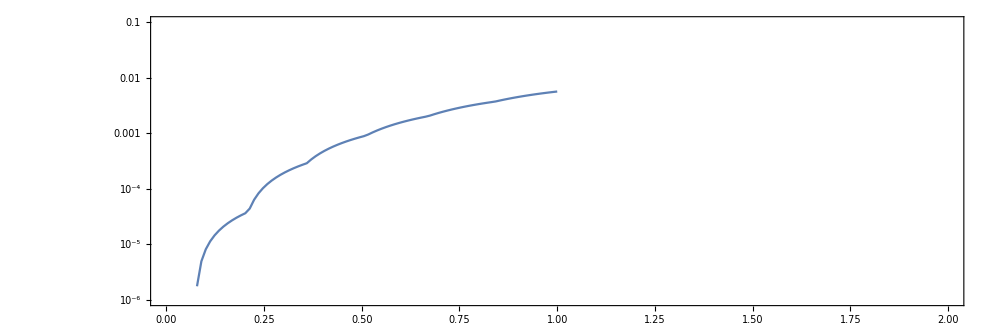

```mathematica
(*Max amplitude list*)
max…amp = List[];

(*Create list of points*)
Do[
AppendTo[
max…amp, 
SortBy[list…of…Omega…zeros[[i]],Im][[-1]]
]
,{i,1,NOmega}
]
xy = Table[{Omega…list[[i]],Im[max…amp[[i]]]},{i,1,NOmega}];

(*Plot data*)
ListLogPlot[xy , AspectRatio->1/3, PlotRange->{{0,2},{10^-6,10^-1}},PlotTheme->"Detailed" , Joined->True]
```

```mathematica
(*Save zeros to files*)
outdata =  Table[{Omega…list[[i]],Re[max…amp[[i]]] ,Im[max…amp[[i]]]  },{i,1,NOmega}];

outname = "data/TM1_rotation_dependence" <>
		"_Rbh_"             <>  ToString[NumberForm[1.0,{5,2}]] <> 
		"_Rc_"               <>  ToString[NumberForm[R0,{5,2}]] <> 
		"_Z_"                 <>  ToString[NumberForm[Z,{5,2}]] <> 
		"_OmegaMax_" <>  ToString[NumberForm[OmegaF,{5,2}]]  <>
		"_mode_"          <> ToString[NumberForm[m,{5,2}]] <>".txt";

Export[
FileNameJoin[{NotebookDirectory[],outname}], outdata , "Table"];
```

### Root dependence on the cavity size

The same procedure used to increase the rotation parameter can be used to probe the behaviour of the roots when the cavity size is increased. We can find the initial roots with a single click now:

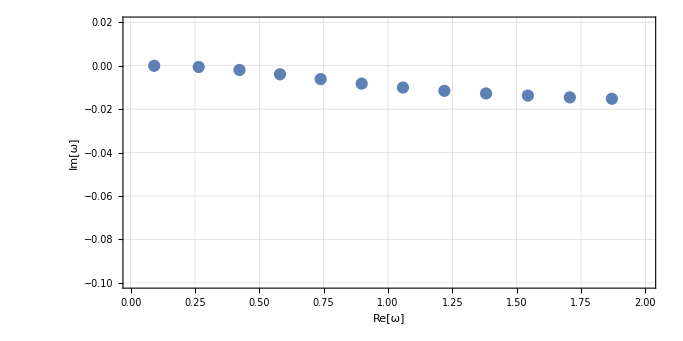

```mathematica
(*Function parameters*)
m = 1;
Ω = 0.0;
R0 =20;
Z = 1.0-I;

(*Region to search for zeros*)
xmin = 0.01;
xmax = 2;
ymin = -0.1;
ymax =0.01;
dx =0.01;
dy=0.005;

(*Find zeros initial zeros*)
startingZeros = get…zero…list[f[R0 , m  , Ω, Z],xmin , xmax ,ymin ,ymax ,dx ,dy];

(*Plot First Zeros*)
ComplexListPlot[
	startingZeros, 
	AspectRatio->1/2,
	PlotRange->{{xmin,xmax},{-0.1,0.02}},
	PlotTheme->"Detailed",
	FrameLabel->{"Re[ω]","Im[ω]"}]
```

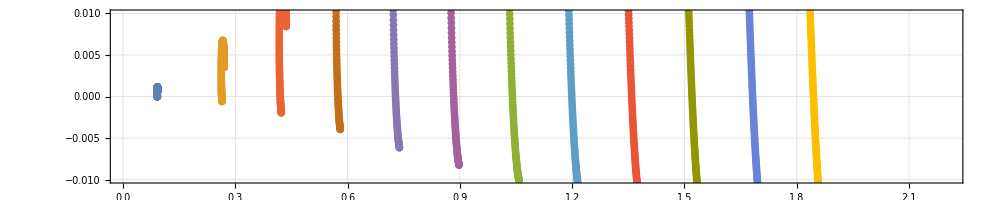

```mathematica
(*Initial zeros*)
list…of…Omega…zeros = List[startingZeros];

(*Rotation Parameters*)
OmegaI = 0.0;
OmegaF = 3.0;
NOmega = 150;
dOmega = (OmegaF -OmegaI)/(NOmega-1);
Omega…list = Table[OmegaI + (i-1)*dOmega,{i,1,NOmega}];

(*Search for sucessive zeros with different alpha parameters*)
Do[
AppendTo[
list…of…Omega…zeros, 
get…zero…list…from[f[R0 , m  , Omega…list[[i]], Z], list…of…Omega…zeros[[-1]]]]
,{i,1,NOmega}
]

(*Plot Result*)
ComplexListPlot[
Transpose[list…of…Omega…zeros],
AspectRatio->1/5,
PlotRange->{{xmin,1.1*xmax},{-0.01,0.01}},
PlotTheme->"Detailed"]
```

The roots “move” quite fast when the cavity size is close to the size of the cylinder so, we must sample much more points near this point. As so, we begin with a certain cavity size and probe things all the way down to when Rc = 1. We then proceed with the inverse search for ever larger cavity sizes.

9

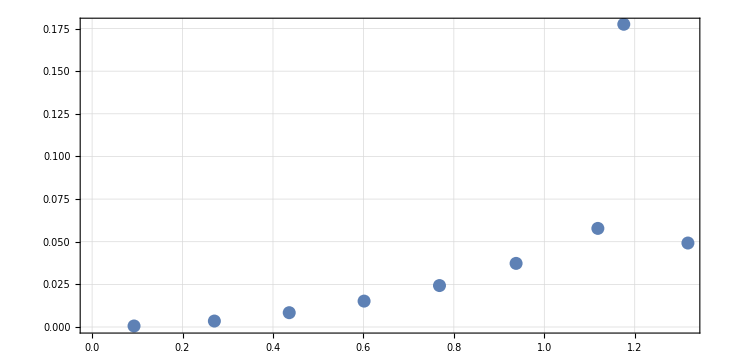

```mathematica
(*Number of roots to track*)
kroot = 9
(*Forward search*)

list…of…Cavity…zeros…FS = 
List[
Table[SortBy[list…of…Omega…zeros[[-1]],Re][[i]],{i,1,kroot}]
];

ComplexListPlot[list…of…Cavity…zeros…FS , AspectRatio->1/2, PlotTheme->"Detailed"]

(*Caviity Radius final value*)
RF = 1.00;
NR = 6000;
dR = (RF -R0)/(NR-1);
R…list…FS = Table[R0 + (i-1)*dR,{i,1,NR}];
```

```mathematica
(*Search for sucessive zeros with different alpha parameters*)
Do[
AppendTo[
list…of…Cavity…zeros…FS, 
get…zero…list…from[f[R…list…FS[[i]] , m  , Omega…list[[-1]], Z], list…of…Cavity…zeros…FS[[-1]]]]
,{i,1,NR}
]
```

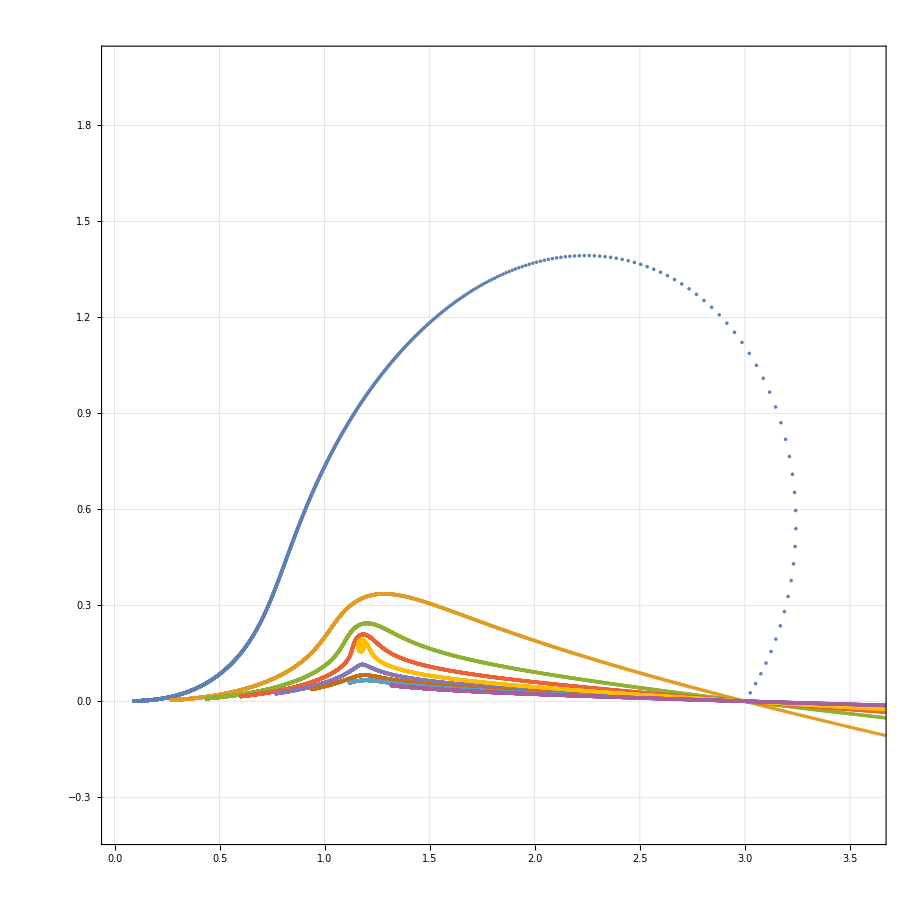

```mathematica
(*Plot Result*)
ComplexListPlot[
Transpose[list…of…Cavity…zeros…FS],
AspectRatio->1,
PlotRange->{{xmin,3.6},{-0.4,2}},
Joined->False,
PlotTheme->"Detailed"]
```

Now onto the Backward search (BS):

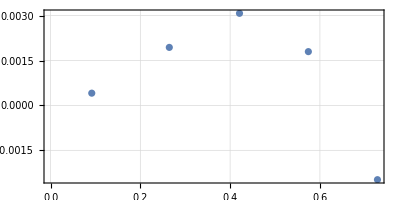

```mathematica
(*Backward search*)
list…of…Cavity…zeros…BS = 
List[
Table[SortBy[list…of…Omega…zeros[[-1]],Re][[i]],{i,1,kroot}]
];

ComplexListPlot[list…of…Cavity…zeros…BS , AspectRatio->1/2, PlotTheme->"Detailed"]

(*Caviity Radius final value*)
RF = 300.00;
NR = 5000;
dR = (RF -R0)/(NR-1);
R…list…BS = Table[R0 + (i-1)*dR,{i,1,NR}];
```

```mathematica
(*Search for sucessive zeros with different alpha parameters*)
Do[
AppendTo[
list…of…Cavity…zeros…BS, 
get…zero…list…from[f[R…list…BS[[i]] , m  , Omega…list[[-1]], Z], list…of…Cavity…zeros…BS[[-1]]]]
,{i,1,NR}
]
```

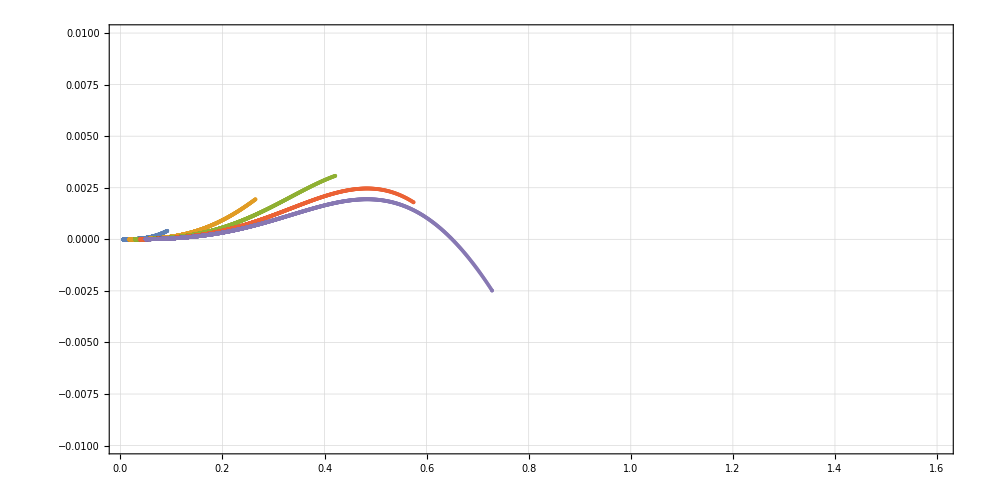

```mathematica
(*Plot Result*)
ComplexListPlot[
Transpose[list…of…Cavity…zeros…BS],
AspectRatio->1/2,
PlotRange->{{xmin,1.6},{-0.01,0.01}},
Joined->False,
PlotTheme->"Detailed"]
```

And we can join the two lists

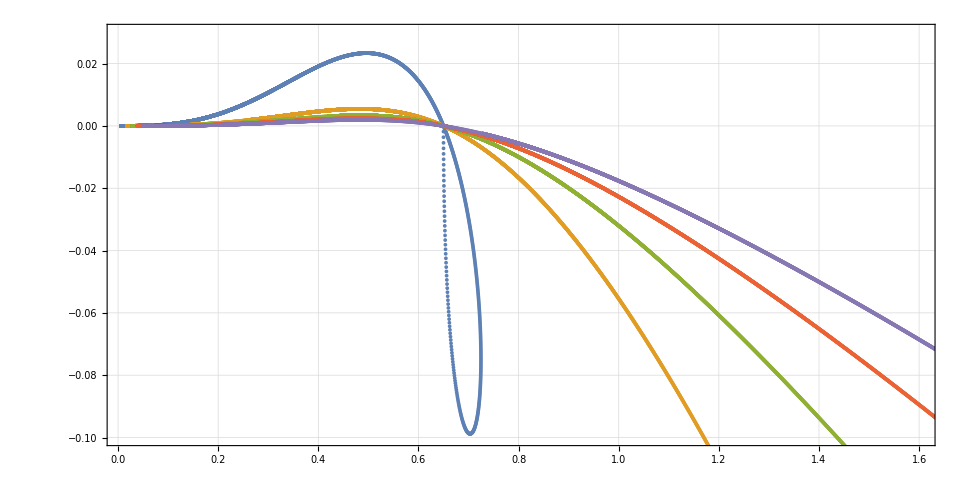

```mathematica
(*Plot Result*)
zero…list = Join[Reverse[Transpose[list…of…Cavity…zeros…BS] ,2], Transpose[list…of…Cavity…zeros…FS] , 2];
(*Plot Result*)
ComplexListPlot[
zero…list,
AspectRatio->1/2,
PlotRange->{{xmin,1.6},{-0.1,0.03}},
Joined->False,
PlotTheme->"Detailed"]
```

and export them

```mathematica
(*Save zeros to files*)
Do[
zero = zero…list[[kzero]];
outdata = Table[{R…list[[j]], Re[zero[[j]]  ] , Im[zero[[j]]] },{j,1,Length[R…list]}];

outname = "data/TM1_CavitySize_Increase_" <>
		"_Rbh_"             <>  ToString[NumberForm[1.0,{5,2}]] <> 
		"_Z_"                 <>  ToString[NumberForm[Z,{5,2}]] <> 
		"_Omega_" <>  ToString[NumberForm[OmegaF,{5,2}]]  <>
		"_mode_"          <>  ToString[NumberForm[m,{5,2}]] <>
		"_Root_"          <> ToString[NumberForm[kzero,{5,2}]] <>
		".txt";

Export[
FileNameJoin[{NotebookDirectory[],outname}], outdata , "Table"];
,{kzero,1,kroot}
]
```

### Root dependence on Impedance value

The next piece of code serves to study the impact of the Impedance value in the solutions to our problem.

```mathematica
(*Function parameters*)
m = 1;
Ω = 0.5;
R0 =30.0;
Z = -1.0I;

(*Region to search for zeros*)
xmin = 0.0;
xmax = 3.0;
ymin = -0.04;
ymax =0.04;
dx =0.05;
dy=0.005;

(*Find zeros*)
startingZeros = get…zero…list[f[R0 , m  , Ω, Z],xmin , xmax ,ymin ,ymax ,dx ,dy];
```

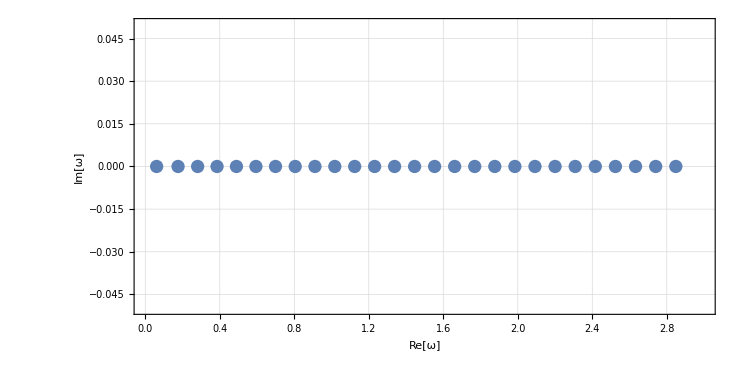

```mathematica
(*Plot First Zeros*)
ComplexListPlot[

	startingZeros, 
	AspectRatio->1/2,
	PlotRange->{{0,3.0},{-0.05,0.05}},
	PlotTheme->"Detailed",
	FrameLabel->{"Re[ω]","Im[ω]"}]
```

To probe the impedance parameter space, we  consider a fixed impedance magnitude and sweep the circle described by it in the complex Z-plane.

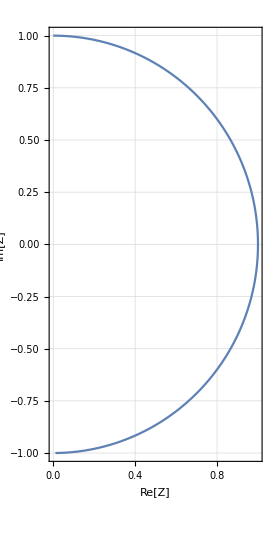

```mathematica
(*Initial zeros*)
list…of…Z…zeros = List[startingZeros];

(*Impedance values*)
Tf = Pi;
Ntheta = 300;
dT= Tf/Ntheta//N;
Z…list = Table[Z*Exp[I*dT*i]//N,{i,1,Ntheta}];

(*Display impedance values*)
ComplexListPlot[Z…list  , PlotTheme->"Detailed", Joined-> True , FrameLabel->{"Re[Z]","Im[Z]"}, AspectRatio->2]
```

```mathematica
(*Search for sucessive zeros with different alpha parameters*)
Do[
AppendTo[
list…of…Z…zeros, 
get…zero…list…from[f[R0 , m  , Ω, Z…list[[i]]], list…of…Z…zeros[[-1]]]]
,{i,1,Ntheta}
]
```

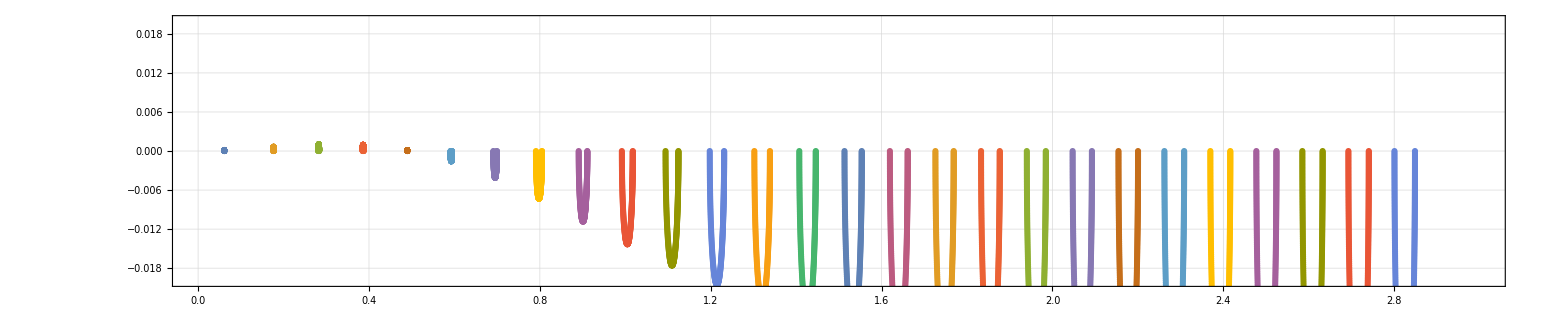

```mathematica
(*Plot Result*)
ComplexListPlot[
Transpose[list…of…Z…zeros],
AspectRatio->1/5,
PlotRange->{{xmin,xmax},{-0.02,0.02}},
PlotTheme->"Detailed"]
```